# SICM in MMA

SICM is Structure and Interpretation of Classical Mechanics, Gerald Jay Sussman and Jack Wisdom, MIT Press, 2001, ISBN 0262194554. This is my version of SICM into Mathematica. I am Brian Beckman. I started this on 31 Aug 2007. I finished it on ...

```mathematica
Clear["Global`*"];
Off[General::spell];
Off[General::spell1];
On[Assert];
```

Convention: Use uncialized camelBack for hyphen-delimited (kebab-case) names. Mathematica doesn't permit hyphens in names. If SICM says "L-free-particle", say lFreeParticle. "Uncialized" means that the first character in the name is uncial (lower case).

## Chapter 1

Preliminaries

A proper setting for analytical mechanics requires the theory of real differentiable manifolds. References for the pieces missing from SICM are
* M. Spivak, Calculus on Manifolds, W.A. Benjamin, Inc, New York, Amsterdam, 1965. 
* David Lovelock and Hanno Rund, Tensors, Differential Forms, and Variational Principles, Wiley, 1975. 
* John H. Hubbard, Barbara Burke Hubbard, Vector Calculus, Linear Algebra, and Differential Forms: A Unified Approach, Prentice Hall, 2001, ISBN-10: 0130414085, ISBN-13: 978-0130414083. 
* Roger Penrose, The Road to Reality: A Complete Guide to the Laws of the Universe, Vintage, 2007, ISBN-10: 0679776311, ISBN-13: 978-0679776314 (semi-technical).
* Kip S. Thorne, Charles W. Misner, John Archibald Wheeler, Gravitation, Freeman, 1973.
* Gerald Jay Sussman, Jack Wisdom, Functional Differential Geometry, MIT Press, https://mitpress.mit.edu/books/functional-differential-geometry.

## Haskell-style Type Notation

The type notation f:T means that f has type T, or (loosely) that f is a member of the set of all T's, which we could also write as f∈T. There are deep differences between types and sets, but they do not concern us here. For our purposes, the only difference between a type and a set is that a set is a value: we can manipulate sets in our programs. Types are at a higher level: we can reason about types in programs, but we don’t have instances of types as data objects in our programs.

Functional types look like this: f:A→B, meaning that f has the type of a function from A to B, meaning (loosely) f is a member of the set of all functions from A to B, a set we write as A→B. A function is a value: it is a member of a set, the set A→B.

Composition converts a pair of compatible functions into a new function that feeds the output of one to the input of the other. If f:A→B and g:B→C, then g∘f is a new function of type A→C. Functions f and g are compatible for the composition g∘f if the output type B of the feeding function f matches the input type B of the eating function g. Composition is a function on functions. ∘ is a low-precedence operator; derivative operators and others bind more tightly.

### Digression on functions

If you are uncomfortable, even slightly, with the definition above, read this section. If you are uncomfortable, even slightly, with the ideas of sets, sets of sets, tuples, tuples of sets, sets of tuples, and so on down the line, go read Naive Set Theory, by Halmos.

We use sets and tuples here without formal definition, with one exception. Mathematica does not have sets, directly. We represent sets via Mathematica Lists. The representation is defective because Mathematica Lists can have duplicate elements and are ordered, and mathematical sets cannot have duplicates and cannot be ordered. We can test a List for for set-ness by sorting and removing duplicates, then asserting whether there is a difference to the original list, sorted.

#### Sets Versus Lists

We honor Mathematica’s convention that functions returning Boolean values have a Q as their last character.

```mathematica
ClearAll[isetQ];
setQ[l_List]:=Sort[Union[l]]===Sort[l];
```

Test it.

```mathematica
setQ@{2,1,3}
```

True

```mathematica
setQ@{1,1,3}
```

False

The empty List represents the empty set, which is a set.

```mathematica
setQ@{}
```

True

Mathematica' s Null is neither a set nor a List, so we don’t use it for an empty set (except maybe in some lousy puns).

```mathematica
setQ@Null
```

setQ[Null]

#### Typography

Terms in boldface, enclosed in square brackets are definitions for this document.

#### Cartesian Product

The [Cartesian product] of sets A and B, written A×B, is the set of all [ordered pairs] or [2-tuples] (a,b) where a is in A and b is in B. A [function from A to B] is a subset f⊂A×B of this Cartesian product A×B that satisfies an additional rule, the [unique-answer rule]: no particular a∈A appears more than once in the first slot of any element of that subset f. The rule guarantees that evaluating f on a particular a, meaning looking up that a in the first slots of the elements of that set of ordered pairs, always yields the same answer: either silence (meaning "no answer"), or the same b∈B. The set of all functions from A to B is the set of all such sets of ordered pairs. Usually, such sets are very large or even uncountably infinite. Let us write a small example. We will build [finite functions], functions that have a finite, countable number of elements.

Let A be the set {Alice, Edna}

```mathematica
A={Alice, Edna}
```

{Alice,Edna}

and let B be the set {Bob, Charles, Dave}.

```mathematica
B={Bob, Charles, Dave}
```

{Bob,Charles,Dave}

The Cartesian product, grouped by members of A, has six members, three choices from B for each choice from A.

```mathematica
(cp=Outer[List,A,B])//TraditionalForm
```

({Alice,Bob} | {Alice,Charles} | {Alice,Dave}
{Edna,Bob} | {Edna,Charles} | {Edna,Dave})

A particular function from A to B is a subset of that Cartesian product that contains no more than one member from each row. How many functions are there? That is the number of ways of choosing no more than one pair from each row. There are four choices for each row: the three explicit ones, plus do not forget the choice that says "no answer." That's four choices for each of two rows, and the total number of functions is 4^2 or 16.

A function that never says "no answer" when you give it an a is a [total function]. A function that might say "no answer" is a [partial function]. Every total function is a partial function.

Simulate no answer by just adding an artificial member to B:

```mathematica
(cp=Outer[List,A,Join[B,{NoAnswer}]])//TraditionalForm
```

({Alice,Bob} | {Alice,Charles} | {Alice,Dave} | {Alice,NoAnswer}
{Edna,Bob} | {Edna,Charles} | {Edna,Dave} | {Edna,NoAnswer})

Form a particular function by picking one pair from each row, something that maps Alice either to a member of B or to NoAnswer and Edna either to a member of B or to NoAnswer. Each row has an entry for every member of A. Here's the set of all sixteen functions; each row in the following is a function from A to B:

```mathematica
(allFunctionsX=Tuples[cp])//TraditionalForm
```

({Alice,Bob} | {Edna,Bob}
{Alice,Bob} | {Edna,Charles}
{Alice,Bob} | {Edna,Dave}
{Alice,Bob} | {Edna,NoAnswer}
{Alice,Charles} | {Edna,Bob}
{Alice,Charles} | {Edna,Charles}
{Alice,Charles} | {Edna,Dave}
{Alice,Charles} | {Edna,NoAnswer}
{Alice,Dave} | {Edna,Bob}
{Alice,Dave} | {Edna,Charles}
{Alice,Dave} | {Edna,Dave}
{Alice,Dave} | {Edna,NoAnswer}
{Alice,NoAnswer} | {Edna,Bob}
{Alice,NoAnswer} | {Edna,Charles}
{Alice,NoAnswer} | {Edna,Dave}
{Alice,NoAnswer} | {Edna,NoAnswer})

NoAnswer is not a member of any set or tuple. We needed it to count the number of partial functions, but it's a fake. Create two new, anonymous Mathematica functions for the clean-up. The innermost anonymous function is #⟦2⟧ =!= Null &.  In that expression, # stands for the [argument] of — the input to — the function, ⟦2⟧ means "pick the second element of whatever is to my left," =!= means "not equal to," and & means "everything to my left is a function." Therefore, #⟦2⟧ =!= NoAnswer & is a function that yields True when its argument — an ordered pair — is a tuple that does not have NoAnswer in its second slot.

Put that first anonymous function in the function-argument slot of Mathematica's built-in Select, which pulls from any list of things those for which Select’s function argument yields True. Create a second anonymous function out of that call of Select by "functionizing" it via # and &: Select[#,(first anonymous function)]&. Map that second anonymous function over our entire list of lists of tuples, that is, our list of all functions. There is one empty function, namely the one where both Edna and Alice pair with NoAnswer. It is the [empty function]; no lookup will succeed on it.

```mathematica
(allFunctions=Map[
Select[#,#⟦2⟧=!=NoAnswer&]&,
allFunctionsX])//MatrixForm
```

({{Alice,Bob},{Edna,Bob}}
{{Alice,Bob},{Edna,Charles}}
{{Alice,Bob},{Edna,Dave}}
{{Alice,Bob}}
{{Alice,Charles},{Edna,Bob}}
{{Alice,Charles},{Edna,Charles}}
{{Alice,Charles},{Edna,Dave}}
{{Alice,Charles}}
{{Alice,Dave},{Edna,Bob}}
{{Alice,Dave},{Edna,Charles}}
{{Alice,Dave},{Edna,Dave}}
{{Alice,Dave}}
{{Edna,Bob}}
{{Edna,Charles}}
{{Edna,Dave}}
{})

Each row above is a partial function, a function that might not yield an answer for some member of A. Some of the partial functions are total.

This doesn't look as pretty as the nice rectangular table, but it is correct and easy to work with.

We're ready to ball that up into a Mathematica function that constructs a list of all of our kinds of (finite) functions from two (finite) sets, in-turn represented by Lists:

```mathematica
findAllFunctions[A_List,B_List]:=
Map[Select[#,#⟦2⟧=!=Null&]&,
Tuples[Outer[List,A,Join[B,{Null}]]]];
```

Test findAllFunctions.

```mathematica
allFunctions==findAllFunctions[A,B]
```

True

When we write “function,” we mean “partial function,” but sometimes, we are not careful to distinguish partial functions from total functions.

In summary, the generalized rule is easy. If A has N members and B has M members, then the set of all (partial) functions from A to B has (M+1)^N members because for each of the N possible inputs, there are M+1 allowable outputs. The number of total functions is M^N.

To remind us of this fact of counting, it is standard to write the set of all total functions from A to B as B^A. In other words, what we write in Haskell as A→B we could also write as B^A (Haskell does not count partial functions in the type A→B). The calculation of the number of functions is trickier when A or B is an infinite set of some kind, but it can be done, and we still write it B^A. See John H. Conway, Numbers and On Numbers and Games for more on infinities.

#### Making Mathematica Functions from Lists of Tuples

Abstractly, a function is a (possibly continuous) list of tuples that obeys the unique-answer rule. We need a Mathematica function that can convert one of our finite functions, as a list of pairs, into something Mathematica can evaluate. The Mathematica built-in Function is one way to make Mathematica functions. Use Select to pick out the unique tuple that matches the argument of Function (we don't check that it is unique, and you can blow this up by feeding it a list of tuples that doesn't satisfy the unique-answer rule). This application of Select returns a list containing one tuple, and we need the first part of that, then we need the second part of that first part, the answer for any a. That's the meaning of the final ⟦1,2⟧. We need a bit of programming detail work to catch and interpret the NoAnswer response.

```mathematica
functionMaker[tuples_List]:=
Function[a,
Module[{tuple=Select[tuples,a===#⟦1⟧&]},
If[tuple==={},{},tuple⟦1,2⟧]]];
```

Test this on a randomly chosen sample from above. aRandomFunction is a function to choose a random function from our list of functions:

```mathematica
ClearAll[aRandomFunction];
aRandomFunction[]:=RandomChoice[allFunctions]
```

Now we can pick a random function from our table of functions and apply it to an argument, say Alice, via ordinary Mathematica function-call syntax with square brackets.

```mathematica
functionMaker[aRandomFunction[]][Alice]
```

Charles

It’s fun to try this over and over. Let’s make a button GUI that can call any function when its button is pressed. Take functionMaker[aRandomFunction[]][Alice] and functionize it by appending & so we can call it over and over:

```mathematica
ClearAll[buttonize];
buttonize[fnRandom_,fnResultFromRandom_:Identity,lbl_:"RANDOMIZE!"]:=
DynamicModule[{val=fnRandom[]},
Manipulate[fnResultFromRandom[val],
Button[lbl,val=fnRandom[]]]];
```

```mathematica
buttonize[functionMaker[aRandomFunction[]][Alice]&]
```

#### Domain and Co-Domain, Actual Domain and Range

If f:A→B, then the set A is the [domain] of f and the set B is the [co-domain] of f. f may not not "hit" every member of B. We must distinguish the [range] of f, the set of all values in B the function actually yields, from the co-domain, B. In general, the range is a subset of the co-domain. Remember that a subset is allowed to be the entire set, so the range is the more general notion: it might be the whole co-domain. Similar observations pertain to the domain. A partial function may not be defined at every element, or even at any element, of its domain. So we introduce [actualDomain], which picks the first element from every pair that makes up the function-as-list-of-pairs. We are guaranteed, by the definition of function and the unique-answer-rule, that there are no duplicates amongst the first elements, so we don’t need to do anything more after picking. We’ll just sort them, for display. We might, out of paranoia, check that there are no duplicates after picking, and we would certainly do so in production-quality software. The goal here, however, is clarity and brevity. We’ll assume there are no duplicates and software depending on this function will fail elsewhere if there are duplicates.

```mathematica
getActualDomain[function_]:=Sort[#⟦1⟧&/@function];
```

The co-domain of a function may have duplicates, so we prune them after picking via Mathematica’s Union.

```mathematica
getCoDomain[function_]:=Union[#⟦2⟧&/@function];
```

Test it on randomly chosen ones:

```mathematica
getActualDomain[aRandomFunction[]]
```

{Alice,Edna}

```mathematica
getCoDomain[aRandomFunction]
```

{Bob,Dave}

#### Injections, Surjections, Bijections, and Inverses.

A function is an [injection] or one-to-one function if no member of its actual range appears more than once. {{Alice, Bob}, {Edna, Bob}} is NOT an injection; {{Alice, Bob}, {Edna, Charles}} is an injection; {{Alice, Null}, {Edna, Null}} is also an injection because Null is not a member of the range (it is not a member of any set), and therefore no member of the range appears more than once. Here's a function to find out if one of our functions is an injection:

```mathematica
isInjection[function_List]:=
Module[{isInjectionQ=Sort[#⟦2⟧&/@function]===getCoDomain[function]},
Print[<|"function"->function,"actual domain"->getActualDomain[function],"co-domain"->getCoDomain[function],"is injection"->isInjectionQ|>];
isInjectionQ];
```

Test it on a randomly chosen function:

```mathematica
isInjection[aRandomFunction]
```

<|function→{{Alice,Charles},{Edna,Charles}},actual domain→{Alice,Edna},co-domain→{Charles},is injection→False|>

False

It's possible to reverse all pairs in an injection and get a new function, for instance {{Bob, Alice}, {Charles, Edna}}. Because no member of the old function's actual range appears more than once, no member of the new function's actual domain appears more than once, and that's all we need to satisfy the unique-answer rule. The new function is the [inverse] of the old injection. The inverse of an injection is a partial function, in general.

```mathematica
invert[function_List]:=
If[isInjection[function],
Reverse/@function,
{}];
```

```mathematica
invert[aRandomFunction]
```

<|function→{{Alice,Bob},{Edna,Bob}},actual domain→{Alice,Edna},co-domain→{Bob},is injection→False|>

{}

IsInjection might be called invertibleToPartialFunctionQ, with the final Q meaning “question” or “query.” It is conventional in Mathematica to end functions that produce only True or False with the letter Q. Such functions are called [predicates].

A [surjection] or "onto" function is a function in which every member of the co-domain appears at least once. We do not have any surjections in our sample because the domain is smaller than the range, and that is a general rule: if the domain is smaller than the range, there will not be any surjections. Write a function to test for surjection, but we can't test it for now:

```mathematica
isSurjection[function_List,range_List]:=
getCoDomain[function]===Union[range];
```

If a function is both an injection and a surjection, then it's a [bijection].

```mathematica
isBijection[function_List,range_List]:=
And[isInjection[function],
isSurjection[function,range]];
```

The inverse of a bijection is a bijection. Bijections are also called [one-to-one correspondences] because they establish a way in which we may think of the domain and range as identical. Such ways of thinking are called [isomorphisms] or [equivalences]. IsBijection might also be called isInvertibleToBijection or just isInvertible.

#### Associativity, Currying, Application, and Partial Evaluation

The Haskell-style functional notation associates to the right, so f:A→B→C=A→(B→C) means that f has type of function from A to the set of functions from B to C. The mathematician's notation goes this way, associating to the left: C^(B^A)=((C^B)^A).

If you have such a function, a function that produces a function, and you want to look up a particular member of C, feed the function first a member of A, getting back a function from B to C, then feed that second function a member of B, to get the final answer. In school, we were taught to think of such a thing as a function of two variables, written f(a,b). This notation is fortunate, because it hints at the deeper fact that f may really be (isomorphic to) a function of one tuple-valued argument.

It turns out beneficial to think of all functions as functions of one argument. This way, we have just one kind of thing in our universe: a function of one argument, rather than many kinds of things: functions of one argument, functions of two arguments, functions of three arguments, and so on. But how can we get from a function of one tuple argument, a function of type (A×B)→C, to a function of one argument that returns a function of one argument, of overall type A→(B→C)? A function of type (A×B)→C returns either Null or a value in C given any 2-tuple of values in A and B, and the same is true of any function of type A→(B→C), so we are free to think of these types as isomorphic. The C on the end and the re-grouping of precedence are critical, however, because A→B is not at all isomorphic to A×B. A→B is the set of all functions from A to B, which is a collection of size B^A of subsets of A×B, the much smaller set of tuples drawn from A and B.

The process of converting functions of tuples to a right-associative chain of functions of one argument is is [Currying]. Belaboring the point, Currying is decomposing functions of multiple variables, or, equivalently, functions of tuples, into chains of functions of single variables. Curry is the surname of Haskell Curry, the logician who came up with this and who also lent his first name to the programming language Haskell.

If we have a (Curried) function f and we wish to find its value for some input argument, a, we must [apply the function to its argument] or [evaluate the function]. In school, we learn to write the value of a function at a particular value of its argument as g=f(a). With Currying, we don't need the parentheses because there is always just one argument, so we write g=f a. It looks just like multiplication. We see later that when f is a linear transformation, then function application is exactly multiplication. But even when f is not linear, the fact that function application looks like multiplication is a good pun.

When the result of function application, g=f a, is, in turn, a function, then the expression f a is a [partial evaluation] of f. Chain your way to the final answer by writing c=g b=f a b. It's not necessary to give the new function a name, as in g=f a, calling it g. In any expressions where g might appear, replace it with f a and the meaning is exactly the same (equivalence under substitution is [referential transparency]). Replacing g everywhere with f a, the name g might as well never have been used to mean f a.

If we insist on writing parentheses with Curried functions, they bunch on (associate to) the left: c=(g b)=(f a) b=((f a) b).

In summary, from the type-assertion f:A→B→C deduce that f a:B→C, and f a b:C when a∈A and b∈B.

#### Avoiding Punning Functions and Their Evaluations

In school, we often do not distinguish between a function f and its value at some argument f(x), here using the old, non-Curried style of parenthesizing. This is a bad pun, because f and f(x) have different types: they are members of different sets. If f:X→Y then f is a member of X→Y, the set of all functions from X to Y, and f(x) is a member of Y. Computers are not smart enough to understand this bad pun, so we must not use it. Computers are not alone, this pun confuses people, too.

```mathematica
Clear[A,B,cp,allFunctionsX,allFunctions,aRandomFunction];
```

Back to classical mechanics, now.

## (1.2) Configuration-Paths, Local Tuples, Lagrangians

Picture something complex like a truck pulling three trailers. Every element of this complicated system entails one or more [degrees of freedom]. Each wheel can rotate freely; its instantaneous angle of rotation is a degree of freedom The hub of each wheel can move up and down on its spring and damper along complex arcs determined by A-arms and other linkages; instantaneous position of center of rotation of each wheel and instantaneous direction of the axis of rotation comprise several more degrees of freedom. Perhaps we account for the flexing of each tire carcass, entailing dozens more degrees of freedom for each tire. Each trailer is free to move about its trailer hitch: more degrees of freedom. Perhaps we account for flex of the trailer structure: potentially hundreds or thousands of more degrees of freedom.

An accounting for the configuration -- the position and orientation of every element of the truck-and-trailer combination — can run to millions of degrees of freedom, depending on the desired fidelity of the model. Each degree of freedom corresponds to a dimension in the configuration space.

In general, [configuration space] is an abstract n-dimensional real differentiable manifold, 𝕄. A point in 𝕄 specifies a particular [configuration] of the system. Each point of 𝕄 implies values for every degree of freedom in the model by a mapping from 𝕄 to ℝ^n.

A [configuration-path function] γ : ℝ→𝕄 is a function of time yielding the configuration at any instant. Its value at some time t∈ℝ is a point in 𝕄, a configuration, i.e., γ(t)∈ 𝕄.

Distinguish γ from the [local tuple] 𝒯[γ], a tuple of functions of time, or, equivalently, a tuple-valued function of time, with however many derivatives we need.

### Derivative

To go further, we must define derivative. The first derivative of γ, written 𝒟γ, is another function of time, one that yields new functions. The value of 𝒟γ at a particular time is a linear transformation from time increments to increments in 𝕄. A [linear transformation] is a particular kind of function where applying it to its argument means multiplying a constant times the argument. We often pun linear transformations, which are functions, against their "constants," which are members of some algebraic structure in which multiplication is defined. Let ℓ be a linear transformation and let t be its argument. Then write ℓ(t)=ℓ*t, punning the linear transformation ℓ with the constant ℓ, and writing multiplication with *. This is a good pun.

What are these constants, more precisely? The short answer for classical mechanics is that each such constant is an n-vector of real numbers, but we get to the answer by a circuitous route. The linear transformation 𝒟γ yields increments in 𝕄. With abstract manifolds like 𝕄, to define increment, we need addition, specifically of points in 𝕄 to increments in 𝕄. To define linear transformation, we need multiplication of increments in 𝕄 by real numbers. Mapping points in 𝕄 to real n-vectors reveals the algebraic structure beneath the manifold: it is a [vector space] over the real numbers (more carefully, the [tangent space] at each point of the manifold is a vector space). Addition in 𝕄 becomes addition of real n-vectors. Multiplication of increments in 𝕄 by arguments of linear transformations becomes multiplication of real n-vectors by real scalars. This prescription generalizes to matrix multiplication when the arguments are not simple scalars: see Spivak and Hubbard.

Once more, formally. 𝒟γ, when applied to a time argument, yields a linear transformation that, when applied to a time increment in turn, yields an abstract increment in 𝕄. These increments in 𝕄 linearly approximate γ in the neighborhood of t, meaning that γ(t+dt)≈γ(t)+𝒟γ(t) * dt, presuming definitions of +, * and ≈ (approximate equality) in 𝕄. Such definitions relate 𝕄 to real vector spaces.

𝒟γ has type ℝ→ℝ→𝕄. Interpret the first ℝ as time, the second ℝ as a time increment, and the final result as an increment in 𝕄. Annotate the type as follows: ℝ_t→ℝ_dt→𝕄_δm. Partially evaluated, 𝒟γ(t):ℝ_dt→𝕄_δm is a rate of change of γ at t, thus accidentally has the same type as γ, ignoring the annotations. Realize that γ(t) has type 𝕄, 𝒟γ(t) has type ℝ_dt→𝕄_δm, and so on to the higher derivatives. The second derivative, 𝒟^2 γ, is a function of time that yields a linear approximation to 𝒟γ(t). Thus, 𝒟^2 γ:ℝ_t→ℝ_dt_1→ℝ_dt_2→𝕄_δm, and 𝒟^2 γ(t):ℝ_dt_1→ℝ_dt_2→𝕄_δm.

𝒯, the local-tuple builder, is a higher-order function. Its type, in pidgin Haskell, is (ℝ_t→𝕄)→ℝ_t→(ℝ_t,𝕄,ℝ_dt→𝕄_δm,ℝ_dt_1→ℝ_dt_2→𝕄_δm...). It takes a configuration function γ:ℝ→𝕄 and returns a tuple-valued function of time, which is isomorphic to a tuple of functions of time

𝒯[γ]:ℝ_t→(ℝ_t,𝕄,ℝ_dt→𝕄_δm,ℝ_dt_1→ℝ_dt_2→𝕄_δm...)=((ℝ_t→ℝ_t),(ℝ_t→𝕄),(ℝ_t→ℝ_dt→𝕄_δm),(ℝ_t→ℝ_dt_1→ℝ_dt_2→𝕄_δm),...)

Abstraction into functions of time obeys a distributive law over the tuple, with the proviso to evaluate every function in the tuple of functions at the same value of the argument, t.

The first slot of 𝒯[γ] contains the identity function, ι:ℝ→ℝ, to capture time data. The second slot of 𝒯[γ] contains just γ; the third slot contains 𝒟γ, and so on.  Leaving off the interpretive annotations,

𝒯[γ]:(ℝ→ℝ,ℝ→𝕄,ℝ→ℝ→𝕄,...) = (ι, γ, 𝒟γ, ...)

The value of the local tuple at time t is:

𝒯[γ](t):(ℝ, 𝕄, ℝ→𝕄,...) = (t, γ(t), 𝒟γ(t), ...)

For brevity, create a short name for the type of the value of the local tuple, namely 𝒯[γ](t):𝔸=(ℝ, 𝕄, ℝ→𝕄,...). The type of 𝒯[γ] is ℝ→𝔸. Consider another function, ℒ:𝔸→ℝ, which maps particular values of the local tuple to a real number.

In practice, ℒ requires only a finite number of elements from 𝒯[γ](t):𝔸, guaranteeing that it measures a local property of the path (page 7, footnote 12; this is a deeper fact having to do with compactness of manifolds: it only works on closed and bounded configuration spaces, not, for instance, on "dusty" spaces or spaces with "long, thin tendrils" and such). This means, however, that we may Curry any particular ℒ across its argument tuple, and think of the first argument of ℒ as a real number, the time; the second argument as a point in 𝕄, a configuration; the third argument as a particular linear transformation in 𝕄, of formal type ℝ_dt→𝕄_δm but punned to its scalar; and so on. In the great majority of cases in physics, ℒ has only these three arguments, effectively depending only on the time, the configuration, and the rate of change of the configuration. It is important, theoretically, to consider ℒs that depend on more derivatives of γ. The Currying of ℒ across its argument tuple is important for developing Euler-Lagrange equations, as in section 1.5 below.

ℒ is the [Lagrangian] and it contains all the physics; 𝒯 is just differential geometry. ℒ∘ 𝒯[γ]:ℝ→ℝ is a real-valued function of time, and the composition checks: (ℒ:𝔸→ℝ)∘(𝒯[γ]:ℝ_t→𝔸)=ℒ∘𝒯[γ]:ℝ_t→ℝ.

For classical mechanics, ℒ∘ 𝒯[γ] is usually a function from time to the kinetic energy minus the potential energy at that instant. Its value at some time is large when the kinetic energy is large and small when the potential energy is large. In geometrical optics, ℒ∘ 𝒯[γ] is, at each instant, the rate of change of the total time it takes light to travel a small distance. In quantum physics, Lagrangians are energy-like, but, in general, account for observables like charge, spin, charm, strangeness, color, flavor, and so on.

Each realm of physical law — classical, quantum, or relativistic — has its own Lagrangians. Usually, physicists invent Lagrangians by ad-hoc intuition, and then test them in the laboratory. Often, particular Lagrangians are just approximations rather than attempts to write exact physical law. There is, however, a hypothesis that all Lagrangians follow from a more primitive information-theoretic theory of measurement. This hypothesis is called Physics from Fisher Information, and I refer you to the eponymous book by B. Roy Frieden, Cambridge University Press, 1999, ISBN-10: 052163167X ISBN-13: 978-0521631679. Here, we  develop each Lagrangian as we need it, in classical fashion.

𝒮[γ](t_1,t_2) = ∫_t_1^t_2 ℒ∘ 𝒯[γ], the integral of ℒ∘ 𝒯[γ] over a particular interval of time is a real number, the [action]. The supreme law of classical mechanics is that action is stationary on a physically realizable path, meaning that a particular γ is the the real configuration function if small variations in γ do not change the value of action.

𝒮, without its arguments, is another higher-order function, of type (ℝ→𝕄)→ℝ→ℝ→ℝ. Give it a configuration-path function and two times, and it will give you a real-number value of action, which can be compared with a lab measurement. Vary the configuration-path function γ a little, and if γ is a realizable, correct, path that we expect to see in the laboratory, the action will not change much.

It is the duty of all theoretical physicists to write all laws of physics, not just of mechanics, in the form of a stationarity principle like this.

## (1.3) Generalized Coordinates and Velocity

Solving a dynamical system means finding a realizable γ over some time domain of interest. In practice, to do calculations, we must get out of the abstract space 𝕄 and into coordinates.

A [coordinate function], χ:𝕄→ℝ^n, maps (open subsets of) 𝕄 to n-tuples of real numbers in ℝ^n. These n-tuples are [generalized coordinates]. (The parenthetical remark about open subsets hides much detail about topology: see the references for this).

A [coordinate path] q=χ∘ γ:ℝ_t→ℝ^n maps time to Real n-tuples. The total time derivative Dq of the coordinate path has type ℝ_t→ℝ_dt→ℝ^n. Dq, partially evaluated at time t, Dq(t):ℝ_dt→ℝ^n, is a linear approximation of q(t), meaning  that q(t) + Dq(t)*dt is a good approximation of q(t+dt) when dt is small. Thus, Dq(t) is the rate of change of q at t. From χ and γ, use the chain rule:

Dq(t)=D(χ∘ γ)(t)≡Dχ(γ(t))∘𝒟γ(t)

Type-checking: Dχ means a mapping from points of 𝕄 to linear approximations of χ:𝕄→ℝ^n (again, a careful accounting requires tangent spaces, fibre bundles and all that; see Penrose, Lovelock & Rund). Therefore, Dχ has type 𝕄→𝕄_δm→ℝ^n. Recall γ(t):𝕄, so Dχ(γ(t)):𝕄_δm→ℝ^n. The composition with 𝒟γ(t):ℝ_dt→𝕄_δm yields Dχ(γ(t))∘𝒟γ(t):ℝ_dt→ℝ^n, which type-checks against Dq (t).

Abstracting time leaves a slightly ugly notation but it type-checks; using the lambda calculus (not defined here):

Dq=D(χ∘ γ)=λ t . Dχ(γ(t))∘𝒟γ(t)  :ℝ_t→ℝ_dt→ℝ^n

That is how we get from the abstract definition of linear approximation:
	γ(t + dt) ≈ γ(t) + 𝒟γ(t) * dt 
to the concrete equation involving real numbers:
	q(t+dt)≈q (t) + Dq(t)*dt
wherewith we know how to do calculations

Dq(t) is the [generalized velocity].

## (1.6) Gamma and Chart (Γ and #)

Let the function Γ map a coordinate path q (t) to a [coordinate representation of the local tuple] by computing derivatives as needed:

Γ[q]:(ℝ→(ℝ,ℝ^n,ℝ→ℝ^n,...))=(ι=id, q, Dq,...)

Γ[q](t):(ℝ,ℝ^n,ℝ→ℝ^n,...)=(t, q(t), Dq(t),...)

Let the function #:(ℝ→(ℝ, 𝕄, ℝ→𝕄,...))⟶(ℝ→(ℝ,ℝ^n,ℝ→ℝ^n,...)) "extend the coordinate representation to the local tuple" by applying the chain rule above as many times as needed:

#(id, γ, 𝒟γ,...)=(id, χ∘ γ,λ t . Dχ(γ(t))∘𝒟γ(t),...)=(ι, q, Dq,...)

# clearly depends on χ, the coordinate function; SICM writes it as #_χ.

Γ[q]=#_χ∘ 𝒯[γ] (Exercise: type-check)

## (p.14) Lagrangian in Generalized Coordinates

Let L_χ=ℒ∘ #_χ^-1. Then L_χ∘ Γ[q]=(ℒ∘ #_χ^-1)∘ (#_χ∘  𝒯[γ])=(ℒ∘ (#_χ^-1∘ #_χ)∘  𝒯[γ])=ℒ∘  𝒯[γ] and

𝒮[γ](t_1,t_2) = ∫_t_1^t_2 ℒ∘ 𝒯[γ]= ∫_t_1^t_2 L_χ∘ Γ[q]

The point is, we must choose coordinates to compute 𝒮[γ](t_1,t_2), but its value does not depend on the particular coordinates chosen. This is critically important and extremely deep. It is foundational for relativity and quantum physics, and very useful in classical physics. Philosophizing, much history of modern physics is in the promotion of this "useful" principle to a "foundational" principle.

Programs

From this point on, we are less careful about distinguishing the abstract verbiage from the coordinate-based verbiage, having made the point that the answers do not depend on particular choices of coordinates. We confidently move between abstract mode and concrete mode, just as a proficient guitarist might sight-read piano music.

## (1.14) Free-Particle Lagrangian

local is a tuple, modeled as a list. Time, Coordinate, and Velocity are pickers:

```mathematica
time[local_]:=local⟦1⟧;
```

```mathematica
coordinate[local_]:=local⟦2⟧;
```

```mathematica
velocity[local_]:=local⟦3⟧;
```

L-free-particle is a (curried) map of [mass] to a [map of local tuple to real], computing Kinetic Energy. A free particle has no potential energy; that is what "free" means. It has only kinetic energy.

```mathematica
lFreeParticle[mass_]:=Function[local,
Module[{v=velocity[local]},mass v.v/2]]
```

A sample "local tuple":

```mathematica
loc1={t,{x,y,z},{Dx,Dy,Dz}}
```

{t,{x,y,z},{Dx,Dy,Dz}}

Apply L-free-particle to a mass m and then to a local tuple, in fact, to the one just defined:

```mathematica
lFreeParticle[m][loc1]
```

1/2 (Dx^2+Dy^2+Dz^2) m

A "coordinate path" is a map of [time] to [a tuple of generalized coordinates].

```mathematica
q=Function[t,{x[t],y[t],z[t]}];
```

```mathematica
q[t0]
```

{x[t0],y[t0],z[t0]}

First derivatives:

```mathematica
D[q[t0],t0]
```

{x'[t0],y'[t0],z'[t0]}

### Digression on derivatives (footnote 31)

Mathematica has several derivative operators. There are some subtle differences. Investigate:

A sample function:

```mathematica
cube=Function[x,x^3]
```

Function[x,x^3]

```mathematica
cube[2]
```

8

Mathematica's D combinator, for partial derivatives, doesn't turn functions into functions, but rather symbolic expressions into symbolic expressions. To feed some function to D, first apply it to a symbolic argument:

```mathematica
cube[ξ]
```

ξ^3

then feed it in:

```mathematica
D[cube[ξ],ξ]
```

3 ξ^2

A better derivative operator would map a function into a function. We can convert a symbolic expression as a function via the /. rule applicator, which effects substitution:

```mathematica
D[cube[z],z]/.z->2
```

12

```mathematica
D[cube[z],z]/.z->ζ
```

3 ζ^2

Thus, we can define a function-to-function derivative operator as follows, being careful about free-variable capture. A free variable is any variable in the body of a function that is not an explicit function argument. When substituting an actual symbolic argument for a function's parameters, the actual argument might collide with pre-existing free variables in the function body. Cube doesn't have any free variables, but we want our new operator to work for functions that might have free variables. Mathematica's Unique returns a symbol guaranteed not to collide with anything:

```mathematica
Df[func_]:=
Module[{fvar=Unique[]},(* guaranteed not to collide with any other variable names that might be hiding in the body of "func" *)
Function[ζ,D[func[fvar],fvar]/.fvar->ζ]]
```

Notice it is not necessary for the argument of Mathematica's built-in Function function — which is a function factory — to be explicitly Unique. Mathematica internally, automatically makes such arguments Unique.

Try Df on cube:

```mathematica
Df[cube]
```

Function[ζ$,∂_fvar$503329 Function[x,x^3][fvar$503329]/.fvar$503329→ζ$]

```mathematica
Df[cube][2]
```

12

Prove Df works even for functions that do have free variables:

```mathematica
sickCube[ζ_]:=ζ^2 z (* z is a free variable *)
```

```mathematica
sickCube[ζ]
```

z ζ^2

```mathematica
sickCube[z] (* collision! free-variable captured (on purpose) *)
```

z^3

Expect Df[sickCube] to calculate the derivative with respect to its argument:

```mathematica
Df[sickCube]
```

Function[ζ$,∂_fvar$504464 sickCube[fvar$504464]/.fvar$504464→ζ$]

Expect 2 ζ z:

```mathematica
Df[sickCube][ζ]
```

2 z ζ

intentionally hit the free-variable; evaluate the derivative at ζ=z; :

```mathematica
Df[sickCube][z]
```

2 z^2

Try it at a numerical argument:

```mathematica
Df[sickCube][2]
```

4 z

Mathematica's Derivative operator creates pretty output, usually, and is nicely curried:

```mathematica
cube'
```

Function[x,3 x^2]

```mathematica
cube'[2]
```

12

```mathematica
sickCube'
```

2 z #1&

Notice the pretty function shorthand: #1 is the first argument and & means "everything in front of me is part of the body of a function." This works around free variables:

```mathematica
sickCube'[ζ]
```

2 z ζ

```mathematica
sickCube'[z]
```

2 z^2

Derivative is short for Derivative[1], meaning compute one derivative with respect to the first argument. Derivative is general: it can calculate any number of derivatives with respect to any number of scalar variables:

```mathematica
Derivative[1][cube]
```

Function[x,3 x^2]

In short hand, that could have been 3#1^2&. However, Mathematica can not test equality of functions (such is undecidable.) We just know they are the same because they have the same values over their entire ranges. Mathematica cannot tell that from the alternative notations:

```mathematica
Function[x,3 x^2]==3#1^2&
```

Function[x,3 x^2]==3 #1^2&

(When Mathematica just repeats your input, it usually means that Mathematica could not find a reduction, that is, Mathematica does not know an answer to your question).

```mathematica
Derivative[1][cube][2]
```

12

When we want the recursive chain rule, Mathematica gives us a "total derivative" operator that turns a function into a function, similarly to our partial-derivative operator, Df:

```mathematica
Dt[cube]
```

Function[x,3 x^2 Dt[x]]

An even better notion of derivative is as in Spivak: the unique linear transformation — of type function — that best approximates the original function incrementally and locally at each point. This is the best generalization of "slope of a tangent" to higher-dimensional spaces. In the familiar one dimension, think of the slope μ of a tangent at a point a as the linear transformation that converts increments dx in the independent variable x of the original function f into increments df of f at a that happen to be good approximations in the sense that f(t+dt)≈f(t)+μ dt.

We may build up such definitions as we go along. For now, remember that Mathematica's partial derivative operator D is just a pure symbolic transformer. It works on arbitrary symbolic expressions, including function applications, as below:

```mathematica
cube2=ξ^3
```

ξ^3

```mathematica
cube2/.ξ->2
```

8

```mathematica
D[cube2,ξ]
```

3 ξ^2

### Digression on The Chain Rule

Assume we know how to calculate the derivatives of f:A→B and g:B→C, namely f':A→A→B, g':B→B→C. What's the derivative of g∘f:A→C? Write f(x+dx)≈f(x)+dx*f'(x), remembering that because f'(x) is a linear transformation, of type A_dx→B, applying it to its argument is the same as multiplying it by its argument. Inserting type annotations, and writing type deductions in horizontal-line notation (premises above, conclusion below), we get

(x:A,dx:A)/(x+dx:A), (f:A→B,x+dx:A)/(f(x+dx):B), (f:A→B, x:A)/(f(x):B), (f':A→A→B,x:A)/(f'(x):A→B), (f'(x):A→B, dx:A)/(dx*f'(x):B)

showing that every term in f(x+dx)≈f(x)+dx*f'(x) is of type B.

Write a similar equation for the linear approximation of g

g(y+dy)≈g(y)+dy*g'(y)

It is clear that every term of type C. Now, substitute f(x) for y, and dx*f'(x) for dy.

g(y)=g(f(x))

dy*g'(y)=dx*f'(x)*g'(f(x))

g(y+dy)=g(f(x)+dy)≈g(f(x))+dx * f'(x) * g'(f(x))

resulting in a definition of (g∘f)', the derivative of (g∘f), in terms of its values x at f(x):

(g∘f)'=λ x . f'(x) * g'(f(x))

Check types

(dx * f'(x):B, g'(f(x)) : B→C)/(dx * f'(x) * g'(f(x)) : C), (dx * f'(x) * g'(f(x)) : C)/(f'(x) * g'(f(x) : A→C), (f'(x) * g'(f(x) : A→C)/(λ x . f'(x) * g'(f(x)) : A→A→C)

((g∘f) : A→C)/((g∘f)' : A→A→C)

## (1.6) Gamma

Gamma maps a q=χ∘ γ [coordinate path] to a [coordinate representation of a local tuple]. It includes the differentiation!

```mathematica
gamma[path_]:=Function[t,(* t is automatically Unique *)
{(* first part of the local description  *)t, 
(* second part of the local description *)path[t], 
(* third part of the local description  *)D[path[t],t]
}];
```

```mathematica
gamma[q]
```

Function[t$,{t$,Function[t,{x[t],y[t],z[t]}][t$],∂_t$ Function[t,{x[t],y[t],z[t]}][t$]}]

```mathematica
gamma[q][t0]
```

{t0,{x[t0],y[t0],z[t0]},{x'[t0],y'[t0],z'[t0]}}

Remember the Lagrangian takes a mass and a coordinate representation of the local tuple:

```mathematica
lFreeParticle[m][gamma[q][t]]
```

1/2 m (x'[t]^2+y'[t]^2+z'[t]^2)

At this point, do not model SICM's up and down distinctions. Lists are lists and they can be dotted freely. We may have to change.

## (p.19) Lagrangian Action

A Lagrangian-action takes a Lagrangian L, a coordinate path q, and endpoint times:

```mathematica
lagrangianAction[L_,q_,t1_,t2_]:=Integrate[L[gamma[q][t]],{t,t1,t2}](* t is automatically Unique and will not capture free variables *)
```

Page 19:

```mathematica
testPath[t_]:={4t+7,3t+5,2t+1}
```

```mathematica
l3=lFreeParticle[3.0];
```

```mathematica
lagrangianAction[l3,testPath,0.,10.]
```

435.

Remember 435; it recurs frequently in downstream tests.

### Exercise 1.4: Lagrangian Actions

Consider the path that goes straight from xa at time ta to xb at time tb. It must be a list because it is a vector even though it is 1-dimensional. Otherwise, it will not type-check, both conceptually — the path is always a vector (list), and computationally — the code squares vectors by dotting them, and dotted scalars do not make sense.

```mathematica
symTestPath[t_]:={xa+(xb-xa)(t-ta)/(tb-ta)}
```

Make sure the test path has the right values at the endpoints:

```mathematica
symTestPath[ta]
```

{xa}

```mathematica
symTestPath[tb]
```

{xb}

The coordinate representation of the local tuple, evaluated at time t:

```mathematica
gamma[symTestPath][t]
```

{t,{xa+((t-ta) (-xa+xb))/(-ta+tb)},{(-xa+xb)/(-ta+tb)}}

Here is the symbolic Lagrangian action of a free particle along this test path:

```mathematica
lagrangianAction[lFreeParticle[m],symTestPath,ta,tb]
```

(m (-xa+xb)^2)/(2 (-ta+tb))

## (p.20) Paths of Minimum Action

Remember the test path. Configuration space is ℝ^3, so this is a 3-vector (3-list). Here's its value at time t:

```mathematica
testPath[t]
```

{7+4 t,5+3 t,1+2 t}

Its value at time 0:

```mathematica
testPath[0]
```

{7,5,1}

Its value at time ten:

```mathematica
testPath[10]
```

{47,35,21}

Here is a plot of the path in 3-space:

```mathematica
ParametricPlot3D[testPath[t],{t,0,10}]
```

-Graphics3D-

Invent an arbitrary variation function into ℝ^3 that we can add to the testPath:

```mathematica
testVariation[t_]:={Sin[t],8Cos[8t],t^2};
```

Force this and all other path variations to vanish at the endpoints of an action integral. Clamp any variation by multiplying by a scale-free quadratic. This is better than the SICM original because the clamping factor, (4(t-t1)(t2-t))/(t2-t1)^2, varies from 0 to 1 no matter what t1 and t2 might be, so long as t1<t2.

```mathematica
clampingFactor[t_,t1_,t2_]:=(4(t-t1)(t2-t))/(t2-t1)^2
```

Every time you evaluate the test expression below, you will get the same y-values and the same shape of curve, but different t1 and t2:

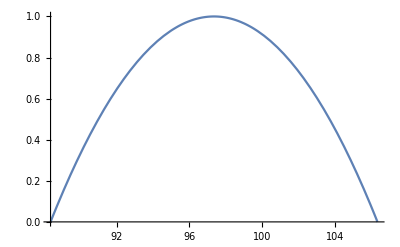

```mathematica
Module[{t1,t2},
t1=RandomReal[{-100,100}];
t2=RandomReal[{t1*1.01,200}];
Plot[clampingFactor[t,t1,t2],{t,t1,t2}]]
```

### Clamped Path Variation

To make a path variation, η(t), that vanishes at the endpoints, multiply any candidate variation function ν(t) by the clamping factor above:

```mathematica
makeη[ν_,t1_,t2_]:=Function[t,clampingFactor[t,t1,t2]*ν[t]]
```

Break from the "style" of SICM footnote 39 here because we do not have addition of functions. Not a big problem though, because (f+g) means Function[t,f(t)+g(t)]

```mathematica
h=makeη[testVariation,0,10]
```

Function[t$,clampingFactor[t$,0,10] testVariation[t$]]

Check that it really does vanish at the endpoints:

```mathematica
h[0]
```

{0,0,0}

```mathematica
h[10]
```

{0,0,0}

The test path is now wiggly, as desired:

```mathematica
ParametricPlot3D[testPath[t]+0.1h[t],{t,0,10}]
```

-Graphics3D-

## (p.21) Varied Free-Particle Action

A varied free-particle action takes a mass, a coordinate path, a candidate variation function, and two endpoints and returns a function of a single real parameter, ϵ, which is a scale factor applied to the clamped variation function. SICM would write the new, varied path as q+ϵ η, but we must write it as λ t. q(t) + ϵ η(t) because we cannot add functions the way we add function values:

```mathematica
variedFreeParticleAction[m_,q_,ν_,t1_,t2_]:=
Function[ϵ,
Module[{η=makeη[ν,t1,t2]},
lagrangianAction[lFreeParticle[m],
Function[t,q[t]+ϵ η[t]],t1,t2]]] (* λ t. q(t) + ϵ η(t) *)
```

Evaluate the variedFreeParticleAction on our test path and test variation, yielding a function of ϵ.

```mathematica
vfpa=variedFreeParticleAction[
3,
testPath,
testVariation,
0,10]
```

Function[ϵ$,Module[{η$=makeη[testVariation,0,10]},lagrangianAction[lFreeParticle[3],Function[t$,testPath[t$]+ϵ$ η$[t$]],0,10]]]

Evaluate that at a particular small value of ϵ.

```mathematica
vfpa[0.1]
```

619.712

That is the action on the putative, wiggly path when ϵ is 0.1.

Where is the imaginary component coming from? Probably integration of Sin & Cos. Investigate. Evaluate the action at a symbolic argument:

```mathematica
vfpa[φ]
```

435-1/560000 φ^2 (-10343840000+1680 Cos[20]-1680 Cos[160]+16632 Sin[20]-134379 Sin[160])

Same thing, only numerically:

```mathematica
N@vfpa[φ]
```

435.+18471.2 φ^2

Notice the magic target number of 435 is hiding in there. Let the symbolic argument go to 0.1:

```mathematica
vfpa[φ]/.φ->0.1
```

619.712

Same as before, just without the "garbage" imaginary part with a coefficient of zero. Try random polynomial variation functions.

```mathematica
randomPolynomialX[minOrder_,maxOrder_,maxAbsCoefficient_]:=
Function[t,
Module[{
order=RandomInteger[{minOrder,maxOrder}],
randomPowerList,
randomCoefficientList},
randomPowerList=Table[t^(i-1),{i,order}];
randomCoefficientList=Table[RandomInteger[
{-maxAbsCoefficient,maxAbsCoefficient}],{order}];
randomCoefficientList.randomPowerList]]
```

```mathematica
randomPolynomialX[3,10,10][t]
```

-6-6 t-t^2-8 t^3+2 t^4-10 t^5-3 t^7

```mathematica
randomPolynomialVector[d_]:=Function[t,
Table[randomPolynomialX[3,10,10][t],{d}]]
```

```mathematica
randomPolynomialVector[3][t]
```

{7+9 t+4 t^2-10 t^4+3 t^5+3 t^6,8-10 t+6 t^2-9 t^3+9 t^4+7 t^5+9 t^6+5 t^7+3 t^8,-8-7 t-t^2-6 t^3+6 t^4+10 t^5+4 t^6+t^7}

```mathematica
variedFreeParticleAction[
3,
testPath,
randomPolynomialVector[3],
0,10][0.1]
```

2.20052×10^15

```mathematica
variedFreeParticleAction[
3,
testPath,
randomPolynomialVector[3],
0,10][φ]
```

435+(53278579355040465904 φ^2)/255255

Now we see why we parameterized by a scalar ϵ: so we can use the built-in minimization library calls in Mathematica to find the minimum value of the action as a function of ϵ.

Page 22:

```mathematica
FindMinimum[vfpa[ϵ],{ϵ,-2}]
```

{435.,{ϵ→0.}}

Try it out with the new, random-polynomial path-variation function:

```mathematica
FindMinimum[
variedFreeParticleAction[
3,
testPath,
randomPolynomialVector[3],
0,10][e],{e,-2}]
```

{435.,{e→0.}}

435, as expected, every time. Chances are we have FindMinimum right.

## (p.22) Finding Trajectories that Minimize the Action

#### Build-up to MakePath

This section is all about shaping data for Mathematica's built-ins. Make-path returns a d-dimensional function of time that traces out the path of the system in configuration space.

To get SICM's linear-interpolants, start with sampling the reals in 1D, then Map that over d dimensions of configuration space.

```mathematica
linearInterpolantsR1[r0_,r1_,howManyIntermediatePoints_]:=
Table[r0+(r1-r0)i/(howManyIntermediatePoints+1),{i,1,howManyIntermediatePoints}]
```

Test: expect the two, evenly spaced intermediate points in [0,1] to be 1/3 and 2/3:

```mathematica
linearInterpolantsR1[0,1,2]
```

{1/3,2/3}

With d as dimensionality of configuration space, map across d-vectors represented as d-lists and transpose into a list of d-vectors:

```mathematica
linearInterpolants[q0_,q1_,n_]:=
Transpose@MapThread[linearInterpolantsR1[#1,#2,n]&,{q0,q1}]
```

We need the following everywhere:

```mathematica
bookendedInterpolants[ζ0_,ζ1_,n_]:=Join[{ζ0},linearInterpolants[ζ0,ζ1,n],{ζ1}]
```

```mathematica
bookendedInterpolantsR1[ζ0_,ζ1_,n_]:=Join[{ζ0},linearInterpolantsR1[ζ0,ζ1,n],{ζ1}]
```

A 3-vector sample from our free-particle test path:

```mathematica
qsxx[n_]:=Module[{q0=testPath[0],q1=testPath[10]},
bookendedInterpolants[q0,q1,n]]
```

Expect evenly-spaced samples along that straight line. Visually inspect five samples:

```mathematica
qsxx[5]// MatrixForm
```

(7 | 5 | 1
41/3 | 10 | 13/3
61/3 | 15 | 23/3
27 | 20 | 11
101/3 | 25 | 43/3
121/3 | 30 | 53/3
47 | 35 | 21)

Plot some larger number of samples, say 17 :

```mathematica
ListPointPlot3D[qsxx[17],Filling->Bottom]
```

-Graphics3D-

Times, sampled at the same rate:

```mathematica
tsxx[n_]:=bookendedInterpolantsR1[0,10,n]
```

```mathematica
tsxx[5]
```

{0,5/3,10/3,5,20/3,25/3,10}

Pick one slice of the coordinate samples, say, the x-components of every d-vector:

```mathematica
Transpose[qsxx[5]]⟦1⟧
```

{7,41/3,61/3,27,101/3,121/3,47}

Pairs of times and components of position, sampled together along the path:

```mathematica
Thread[{tsxx[5],Transpose[qsxx[5]]⟦1⟧}]//MatrixForm
```

(0 | 7
5/3 | 41/3
10/3 | 61/3
5 | 27
20/3 | 101/3
25/3 | 121/3
10 | 47)

A function for doing likewise for any component slice:

```mathematica
qsxxD[n_]=Function[d,Thread[{tsxx[n],Transpose[qsxx[n]]⟦d⟧}]]
```

Function[d,Thread[{tsxx[n],Transpose[qsxx[n]]⟦d⟧}]]

Build back a list of pairs with time samples threaded along with the component samples. This is the shape needed for Mathematica's built-in functions:

```mathematica
Map[qsxxD[5],{1,2,3}]//MatrixForm
```

{{{0,7},{5/3,41/3},{10/3,61/3},{5,27},{20/3,101/3},{25/3,121/3},{10,47}},{{0,5},{5/3,10},{10/3,15},{5,20},{20/3,25},{25/3,30},{10,35}},{{0,1},{5/3,13/3},{10/3,23/3},{5,11},{20/3,43/3},{25/3,53/3},{10,21}}}

Abstract one level so we can get the same kind of shape for any number of samples:

```mathematica
samplesAndTimesXX[n_]:=Map[qsxxD[n], {1,2,3}]
```

And test:

```mathematica
samplesAndTimesXX[5]//MatrixForm
```

((0
7) | (5/3
41/3) | (10/3
61/3) | (5
27) | (20/3
101/3) | (25/3
121/3) | (10
47)
(0
5) | (5/3
10) | (10/3
15) | (5
20) | (20/3
25) | (25/3
30) | (10
35)
(0
1) | (5/3
13/3) | (10/3
23/3) | (5
11) | (20/3
43/3) | (25/3
53/3) | (10
21))

As another check, get the Lagrangian interpolation polynomial for the x component along the path. Expect the original linear polynomial describing the path at the outset. ("Lagrangian" here does not mean the physics Lagrangian; it means a kind of polynomial invented by the same Mr. Lagrange: a small polynomial guaranteed to go through a given set of data points):

```mathematica
InterpolatingPolynomial[qsxxD[5][1],t]
```

7+4 t

Three Lagrangian interpolation functions (actually symbolic expressions on which we must use "rules" for substitution, but good enough; the digression on derivatives above showed how to convert symbolic expressions into functions using rules):

```mathematica
Map[InterpolatingPolynomial[#,t]&,samplesAndTimesXX[5]]
```

{7+4 t,5+3 t,1+2 t}

Expect the same answer given any number of samples:

```mathematica
Map[InterpolatingPolynomial[#,t]&,samplesAndTimesXX[34]]
```

{7+4 t,5+3 t,1+2 t}

Wrap all that up into a version of SICM's makePath. From now on, qs may not be linear.

### (p.22) Make Path

Make Lagrangian interpolating polynomials for each dimension given endpoints and intermediate values of the qs. Each intermediate q is a d-vector. Sample the times evenly. Returns a function from time to ℝ^d, of type ℝ→ℝ^d.

```mathematica
makePath[t0_, q0_, t1_, q1_, qs_]:=Module[
{dims=Length[q0], (* works for any dimensionality *)
ts=bookendedInterpolantsR1[t0,t1,Length[qs]],(* samples times evenly *)
qts=Transpose[Join[{q0},qs,{q1}]], (* n+2 list of d-vectors *)
sts, (* new samples and times *)
ips, (* new interpolating polynomials *)
w=Unique[]},(* avoid free-var capture *)
sts=Map[Thread[{ts,qts⟦#⟧}]&,Range[dims]];
(* That is a d-list of time/q-component pairs *)
ips=Map[InterpolatingPolynomial[#,w]&,sts];
(* A d-list of interpolating polynomials, the polynomial's variable is w == Some Unique *)
Function[u,ips/.w->u] (* convert the symbolic polynomial to function *) ]
(* Returns a d-dimensional function of time *)
```

Check that makePath gives the original linear path equations over the linear test data.

```mathematica
(innerQs=linearInterpolants[testPath[0],testPath[10],5])//MatrixForm
```

(41/3 | 10 | 13/3
61/3 | 15 | 23/3
27 | 20 | 11
101/3 | 25 | 43/3
121/3 | 30 | 53/3)

```mathematica
N@innerQs//MatrixForm
```

(13.6667 | 10. | 4.33333
20.3333 | 15. | 7.66667
27. | 20. | 11.
33.6667 | 25. | 14.3333
40.3333 | 30. | 17.6667)

Check at time t:

```mathematica
tpxx=makePath[0,testPath[0],10,testPath[10],innerQs];
```

```mathematica
tpxx[t]
```

{7+4 t,5+3 t,1+2 t}

Check the endpoints:

```mathematica
tpxx[0]
```

{7,5,1}

```mathematica
tpxx[10]
```

{47,35,21}

#### Scrunched-up version

A scrunched-up version of makePath is as follows. I do not recommend this style of programming because the reader must tease it all apart and reproduce an un-scrunched version to understand it. However, the scrunched-up style avoids temporary variables and some authors favor it.

```mathematica
makePath2[t0_, q0_, t1_, q1_, qs_]:=
Module[{w=Unique[]},
Function[u,
Map[InterpolatingPolynomial[#,w]&,
Map[Thread[{
bookendedInterpolantsR1[t0,t1,Length[qs]],
Transpose[Join[{q0},qs,{q1}]]⟦#⟧}]&,
Range[Length[q0]]]]/.w->u]]
```

Test:

```mathematica
makePath2[0,testPath[0],10,testPath[10],innerQs][t]
```

{7+4 t,5+3 t,1+2 t}

### (p.23) Parametric Path Action

A [parametric path action] takes a Lagrangian and endpoints, and returns a function of a collection of qs. Given a list of d-vector samples along a path evenly sampled in time, this integrates the Lagrangian over an interpolating polynomial approximating that path and returns the resulting action value.

```mathematica
parametricPathAction[lagrangian_,t0_,q0_,t1_,q1_]:=
Function[qs,
lagrangianAction[
lagrangian,
makePath[t0,q0,t1,q1,qs],
t0,t1]]
```

Parametric path action applied to the old test path, expecting our lucky number "435:"

```mathematica
ppaXX=parametricPathAction[
lFreeParticle[3],
0,testPath[0],
10,testPath[10]];
```

```mathematica
ppaXX[innerQs]
```

435

### (p.23) Find Path

The parametric path action (ppa) is a function of initial qs to ℝ, the value of the action. The qs are an n-list of d-vectors (see qsxx[n]), where d is the dimensionality of configuration space and n is the number of samples: qs∈(ℝ^d)^n=ℝ^(d n). multidimensional-minimize finds the particular d-vector values of the qs — the particular member of ℝ^(d n) — that minimize(s) the ppa. Mathematica's FindMinimum does the work for us, just needing repackaging of the input variables as a flattened list.

Suppose we have a list of d n variables or values. Partition those as an n-list of d-vectors for ppa, inverting Flatten:

```mathematica
innerQs==Partition[Flatten[innerQs],3]
```

True

#### multidimensional-minimize

Convert a ppa into a function that takes flattened variables or values, members of ℝ^(d n), precondition for Mathematica's FindMinimum:

```mathematica
convertedPPA[ppa_,varsOrValues_,d_]:=
ppa[Partition[varsOrValues,d]]
```

Take a list of initial qs, construct variables for it, and minimize the convertedPPA over that list of variables starting with the given initial values.

Our solution calls parametricPathAction just once eagerly to construct a symbolic interpolating polynomial for the action. FindMinimum finds the values of those symbolic coefficients that minimize that polynomial. This is different from SICM's solution , which calls parametricPathAction numerically in the inner loop of their minimizer. We revisit this point in exercise 1.5, below, wherein we instrument FindMinimum to watch it in action.

```mathematica
multidimensionalMinimize[ppa_,initQs_]:=Module[
{dims,flats,vars,initPairs},
dims=Length[initQs⟦1⟧];
flats=Flatten[initQs];
vars=Table[Unique[],{Length[flats]}];(* new free vars *)
initPairs=Transpose[{vars,flats}];
FindMinimum[convertedPPA[ppa,vars,dims],initPairs]]
```

The result is a set of rules giving the numerical values of symbolic coefficients that minimize the parametric path action:

```mathematica
testXX=multidimensionalMinimize[ppaXX,innerQs]
```

{435.,{$115→13.6667,$116→10.,$117→4.33333,$119→20.3333,$120→15.,$121→7.66667,$122→27.,$123→20.,$124→11.,$125→33.6667,$126→25.,$127→14.3333,$128→40.3333,$129→30.,$131→17.6667}}

Pick out the rule mapping and repack it back into a list of 3-vectors. Expect it to find exactly innerQs for the linear test data:

```mathematica
Partition[Map[#⟦2⟧&,testXX⟦2⟧],3]//MatrixForm(* pick out coefficients *)
```

(13.6667 | 10. | 4.33333
20.3333 | 15. | 7.66667
27. | 20. | 11.
33.6667 | 25. | 14.3333
40.3333 | 30. | 17.6667)

```mathematica
N@innerQs//MatrixForm
```

(13.6667 | 10. | 4.33333
20.3333 | 15. | 7.66667
27. | 20. | 11.
33.6667 | 25. | 14.3333
40.3333 | 30. | 17.6667)

FindMinimum has found the particular values of the 15 independent variables of the paramaterized path that minimizes the action.

The last step is to return make-path applied once more to those particular actual minimizing values, appropriately reformatted. This returns a function of one real variable to ℝ^d, represented as a list of functions. A one-dimensional path will be a list of one function. A three-dimensional path will be a list of three functions. To inspect the list, apply the function to a symbolic or numerical argument in square brackets, as is usual in Mathematica:

```mathematica
findPath[lagrangian_,t0_,q0_,t1_,q1_,n_]:=
Module[{d,initialQs,ppa,minimizingQs,repackedQs},
d=Length[q0];
initialQs=linearInterpolants[q0,q1,n];
ppa=parametricPathAction[lagrangian,t0,q0,t1,q1];
minimizingQs=multidimensionalMinimize[ppa,initialQs];
repackedQs=Partition[Map[#⟦2⟧&,minimizingQs⟦2⟧],d];
makePath[t0,q0,t1,q1,repackedQs]]
```

```mathematica
Expand@Chop@
Timing[findPath[
lFreeParticle[3],
0,testPath[0],
10,testPath[10],
5][t]]
```

{9.0625,{7+4 t,5.+3. t,1+2 t}}

Glorious! The linear path is the minimal-action path.

Computing numerically rather than symbolically, FindMinimum complains that it cannot get the function to decrease. That is plausible because we already know our input linear path is the minimal path. With the harmonic oscillator, below, the speed just increases and we do not get this problem:

```mathematica
Chop[
Expand@Timing[findPath[
lFreeParticle[3.],
0,testPath[0.],
10.,testPath[10.],
5][t]],10^-6]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{1.125,{7.+4. t-1.38831×10^-6 t^2,5.+3. t,1.+2. t}}

## (p.24) Harmonic Oscillator Sample

Undamped harmonic oscillator L(t,q,v)=1/2 m v^2-1/2 k q^2:

```mathematica
lHarmonic[m_,k_]:=
Function[local,
Module[{
q=coordinate[local],
v=velocity[local]},
1/2 m v.v-1/2 k q.q]]
```

```mathematica
Timing[q=findPath[
lHarmonic[1,1],
(* t0 *) 0,
(* q0 *) {1},
(* t1 *) Pi/2,
(* q1 *) {0},
(* n  *) 3] ]
```

{3.73438,Function[u$,ips$637785/.w$637785→u$]}

```mathematica
q[t]
```

{1+t (-0.194116+(-π/8+t) (-0.455364+(-π/4+t) (0.090369+0.0284653 (-(3 π)/8+t))))}

12x faster if we do up-front numeric computation rather than all symbolic:

```mathematica
Timing[q=findPath[
lHarmonic[1.,1.],
(* t0 *) 0.,
(* q0 *) {1.},
(* t1 *) N[Pi/2],
(* q1 *) {0.},
(* n  *) 3] ]
```

{0.15625,Function[u$,ips$638757/.w$638757→u$]}

```mathematica
Expand[q[t]]
```

{1.+0.00223389 t-0.513541 t^2+0.0232991 t^3+0.0284653 t^4}

The output is a list because we represent all paths, even in ℝ^1, as lists, so the same code will work in any number of dimensions. Mathematica's plotting is smart about this:

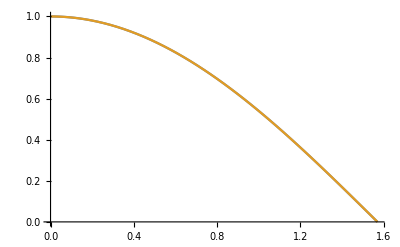

```mathematica
Plot[{q[t],Cos[t]},{t,0,Pi/2}]
```

The following reproduces Figure 1.1:

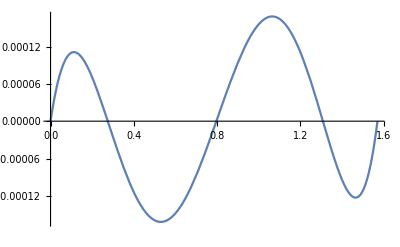

```mathematica
Plot[q[t]-Cos[t],{t,0,Pi/2}]
```

The following is a realization of the last paragraph on p.24, which the authors do not plot, showing that increasing the order of the approximation by one increases the accuracy by a factor of 15:

```mathematica
Timing[r=findPath[lHarmonic[1.,1.],0.,{1.},Pi/2,{0.},4]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.3125,Function[u$,ips$641114/.w$641114→u$]}

```mathematica
Expand@Chop@N@r[t]
```

{1.-0.000231642 t-0.49773 t^2-0.00697064 t^3+0.050963 t^4-0.00572897 t^5}

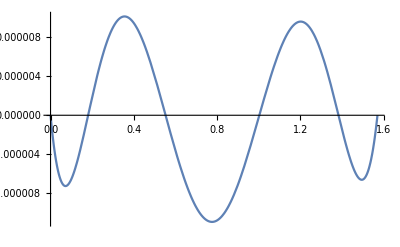

```mathematica
Plot[r[t]-Cos[t],{t,0,Pi/2}]
```

## (Ex 1.5) Solution Process

To watch the solution process, Sow intermediate path values, Reap them, reconstruct the internal (and opaque) interpolating polynomials, and Plot them. First, rewrite multidimensionalMinimize to Sow:

```mathematica
multidimensionalMinimize[ppa_, initQs_] := Module[
  {dims, flats, vars, initPairs},
  dims = Length[initQs⟦1⟧];
  flats = Flatten[initQs];
  vars = Table[Unique[], {Length[flats]}];(* new free vars *)
  initPairs = Transpose[{vars, flats}];
  FindMinimum[convertedPPA[ppa, vars, dims], initPairs,
   StepMonitor :> Sow[vars]]](* the only new stuff is here <— *)
```

Now reap:

```mathematica
(happyJoy = Reap[findPath[
     lHarmonic[1., 1.],
     (* t0 *) 0.,
     (* q0 *) {1.},
     (* t1 *) N[Pi/2],
     (* q1 *) {0.},
     (* n  *) 3] ]) // OutputForm
```

{Function[u$, ips$642602 /. w$642602 -> u$], 
 
  {{{0.804027, 0.513507, 0.268009}, 
 
    {0.889933, 0.614455, 0.283504}, 
 
    {0.909454, 0.664262, 0.334386}, 
 
    {0.923803, 0.707131, 0.382812}, 
 
    {0.923771, 0.707096, 0.382811}, {0.923771, 0.707096, 0.382811}}
 
    }}

Fish out the stream of intermediate values of the lost polynomials:

```mathematica
joys1 = happyJoy[[2, 1]]
```

{{0.804027,0.513507,0.268009},{0.889933,0.614455,0.283504},{0.909454,0.664262,0.334386},{0.923803,0.707131,0.382812},{0.923771,0.707096,0.382811},{0.923771,0.707096,0.382811}}

Bookend the values at the fixed endpoints:

```mathematica
joys2 = Map[Join[{1.}, #, {0.}] &, joys1]
```

{{1.,0.804027,0.513507,0.268009,0.},{1.,0.889933,0.614455,0.283504,0.},{1.,0.909454,0.664262,0.334386,0.},{1.,0.923803,0.707131,0.382812,0.},{1.,0.923771,0.707096,0.382811,0.},{1.,0.923771,0.707096,0.382811,0.}}

Recreate the independent variables:

```mathematica
tees2 = bookendedInterpolantsR1[0, Pi/2, 3]
```

{0,π/8,π/4,(3 π)/8,π/2}

Reconstruct the pairs of independent variables and values:

```mathematica
joys25 = Map[Thread[{tees2, #}] &, joys2]
```

{{{0,1.},{π/8,0.804027},{π/4,0.513507},{(3 π)/8,0.268009},{π/2,0.}},{{0,1.},{π/8,0.889933},{π/4,0.614455},{(3 π)/8,0.283504},{π/2,0.}},{{0,1.},{π/8,0.909454},{π/4,0.664262},{(3 π)/8,0.334386},{π/2,0.}},{{0,1.},{π/8,0.923803},{π/4,0.707131},{(3 π)/8,0.382812},{π/2,0.}},{{0,1.},{π/8,0.923771},{π/4,0.707096},{(3 π)/8,0.382811},{π/2,0.}},{{0,1.},{π/8,0.923771},{π/4,0.707096},{(3 π)/8,0.382811},{π/2,0.}}}

Reconstruct the lost polynomials:

```mathematica
joys3 = Expand@Map[InterpolatingPolynomial[#, t] &, joys25]
```

{1.-0.128339 t-1.37461 t^2+1.23909 t^3-0.362861 t^4,1.+0.0281076 t-0.913606 t^2+0.331525 t^3-0.0122928 t^4,1.+0.0192112 t-0.697888 t^2+0.150386 t^3+0.0178927 t^4,1.+0.00229743 t-0.513381 t^2+0.0229582 t^3+0.0286015 t^4,1.+0.00223434 t-0.513539 t^2+0.0232965 t^3+0.0284664 t^4,1.+0.00223389 t-0.513541 t^2+0.0232991 t^3+0.0284653 t^4}

Finally plot the list of them:

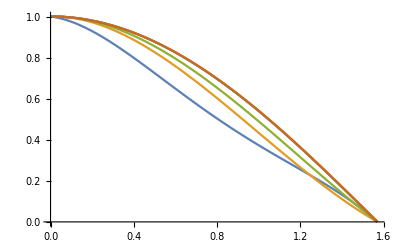

```mathematica
Plot[joys3, {t, 0, Pi/2}]
```

How about a packaged-up version, now, that plots the intermediate polynomials for any order?

```mathematica
plottingFindPath[lagrangian_, t0_, q0_, t1_, q1_, n_] :=Module[{happyJoy = Reap[findPath[lagrangian, t0, q0, t1, q1, n]],
   joys1, joys2, tees2, joys25, joys3},
  joys1 = happyJoy⟦2, 1⟧;
  joys2 = Map[Join[q0, #, q1] &, joys1];
  tees2 = bookendedInterpolantsR1[t0, t1, n];
  joys25 = Map[Thread[{tees2, #}] &, joys2];
  joys3 = Expand@Map[InterpolatingPolynomial[#, t] &, joys25];
  Plot[joys3, {t, t0, t1}]]
```

Scrunch it up, just for fun. As an aside, the above corresponds to Haskell "do" notation for monadic sequences, the below corresponds to an equivalent explicit nesting of function calls. Because of Plot' s peculiar evaluation rules, we must have one variable defined, otherwise colors will not display properly. This computation is not really monadic because it is not purely functional.

```mathematica
plottingFindPath[lagrangian_, t0_, q0_, t1_, q1_, n_] :=Module[{j = Expand@Map[InterpolatingPolynomial[#, t] &, Map[Thread[{bookendedInterpolantsR1[t0, t1, n], #}] &, Map[Join[q0, #, q1] &, Reap[findPath[lagrangian, t0, q0, t1, q1, n]]⟦2, 1⟧]]]},
  Plot[j, {t, t0, t1}]]
```

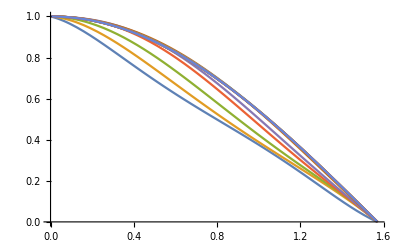

```mathematica
plottingFindPath[lHarmonic[1., 1.],
 (* t0 *) 0.,
 (* q0 *) {1.},
 (* t1 *) N[Pi/2],
 (* q1 *) {0.},
 (* n  *) 4]
```

## (Ex 1.6) Impossible Path (undone)?

What happens if we specify an inconsistency at the endpoints? Go back to the free-particle Lagrangian:

```mathematica
Expand@Chop@findPath[
lFreeParticle[3],
0,testPath[0],
10,testPath[10],
5][t]
```

{7+4 t,5.+3. t,1+2 t}

There's no easy way to substitute in irregularities. We need a version of the software stack that creates impossible paths. Scrunch things up to get everything in one place and in view:

```mathematica
multiMin2[ppa_, initQs_] := 
Module[{flats= Flatten[initQs], vars},
  vars = Table[Unique[], {Length[flats]}];
  FindMinimum[ppa[Partition[vars, Length[initQs⟦1⟧]]], 
Transpose[{vars, flats}],
   StepMonitor :> Sow[vars]]]
```

```mathematica
findPath2[L_,t0_,q0_,t1_,q1_,n_]:=
makePath[t0,q0,t1,q1,
Partition[
Map[#⟦2⟧&,
multiMin2[
Function[qs,
lagrangianAction[L,
makePath[t0,q0,t1,q1,qs],t0,t1]],
linearInterpolants[q0,q1,n]]⟦2⟧],
Length[q0]]]
```

```mathematica
Expand@
Chop@
findPath2[lFreeParticle[3],
0,testPath[0],
10,testPath[10],3][t]
```

{7.+4. t,5.+3. t,1.+2. t}

## (1.5) Euler-Lagrange Equations

```mathematica
Clear[e1,e2,t,q,p,dq,f,g,h,ll,LcΓ]
```

Recall that the Lagrangian, ℒ, is a function of the local tuple, 𝒯[γ], evaluated at some instant of time, so that ℒ∘𝒯[γ] is a real-valued function of time, of type ℝ→ℝ. ℒ takes a finite number of values and computes a real number from them. Here's the undamped harmonic oscillator, once again, in a slightly different format from

```mathematica
LcΓ [t_,q_,dq_]:=1/2 m dq^2-1/2 k q^2
```

```mathematica
e1=Dt[Derivative[0,0,1][LcΓ][t,q,p],t]-Derivative[0,1,0][LcΓ][t,q,p]
```

k q+p Dt[m,t]+m Dt[p,t]

```mathematica
e2=((e1/.q->q[t])/.p->q'[t])/.Dt[m,t]->0
```

k q[t]+m q''[t]

```mathematica
DSolve[e2==0,q[t],t]
```

{{q[t]→C[1] Cos[(√k t)/(√m)]+C[2] Sin[(√k t)/(√m)]}}

```mathematica
Clear[e1,e2,t,q,p,dq,f,g,h,ll,LcΓ]
```